```mathematica
(* Temperature in a building is modeled by the ODE 'Temp' below. T(t) is the temperature in the building at time t. Ta is the ambient temperature ouside the building, Tw is the desired temperature,and P is the rate of change of T. k are negative constants, typically between -5 and -0.5. *)
```

```mathematica
k1 = -0.9;
k2= -0.8;
Ta = 55;
Tw = 72;
P = 10;
Temp = T'[t] == k1(T[t]-Ta)+k2(T[t]-Tw)+P;

(* For constant variables, the solution to the ODE is simple. Depending on the initial condition of T, the solution will either increase or decrease to Tw quickly. *)
sol = DSolve[{Temp,T[0]==0},T[t],{t,0,24}]
```

{{T[t]→68.8824-68.8824 ⅇ^(-1.7 t)}}

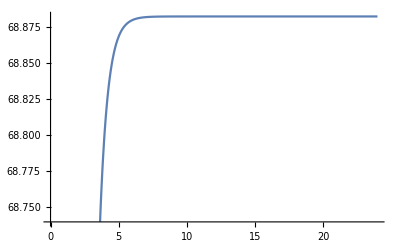

```mathematica
Plot[Evaluate[T[t]]/.sol,{t,0,24}]
```

```mathematica
(* Consider a situation where Ta is not constant, but a variable periodic function. Still, the solution quickly converges to Tw. *)
Ta = 10-c*cos(t*pi/24);
sol1 = DSolve[{Temp,T[0]==100},T[t],{t,0,24}]
```

{{T[t]→68.8824+31.1176 ⅇ^(-1.7 t)}}

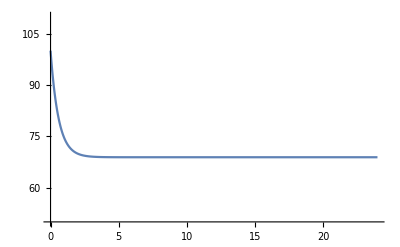

```mathematica
Plot[Evaluate[T[t]]/. sol1,{t,0,24},PlotRange->{50,110}]
```

```mathematica
(* Now consider where Ta is constant, but the rate of change variable P is periodic. Now, the solution no longer directly converges to Tw, but rather oscillates around Tw periodically. *)
Ta = 55;
P2[t_]:=0.5Cos[t];
Temp2 = T2'[t] == k1(T2[t]-Ta)+k2(T2[t]-Tw)+P2[t];
sol2 = NDSolve[{Temp2,T2[0]==80},T2[t],{t,0,24}]
```

{{T2[t]→InterpolatingFunction[…][t]}}

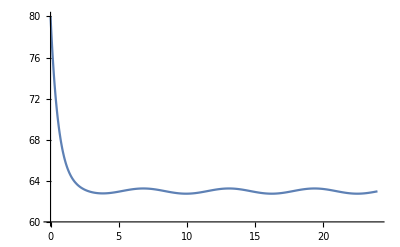

```mathematica
Plot[Evaluate[T2[t]]/.sol2,{t,0,24},PlotRange->{60,80}]
```

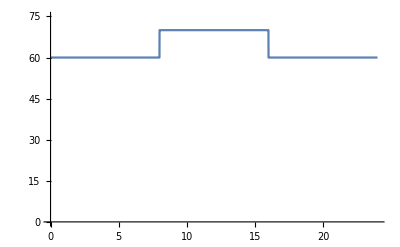

```mathematica
(* Also consider when Tw is periodic. In this model, Tw increases from t=8 to t=15, similar to how businesses may heat/cool their building less outside of regular business hours. In this model, Tw appears non periodic because we only graph one period, but in a larger implementation, longer times, and thus multiple periods, would be modeled. P is still periodic as in the last model. *)
TW[t_]:=  10HeavisidePi[(t-12)/8]+60;
Plot[TW[t],{t,0,24},PlotRange->{0,75}]
```

```mathematica
Temp3 = T3'[t] == k1(T3[t]-Ta)+k2(T3[t]-TW[t])+P2[t];
sol3 = NDSolve[{Temp3,T3[0]==80},T3[t],{t,0,72}]
```

{{T3[t]→InterpolatingFunction[…][t]}}

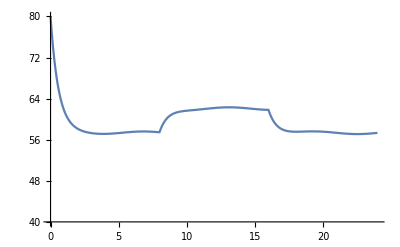

```mathematica
Plot[Evaluate[T3[t]]/.sol3,{t,0,24},PlotRange->{40,80}]
```

```mathematica
(* We see the solution curve recognizes our non-constant Tw, and changes appropriately.*)
```

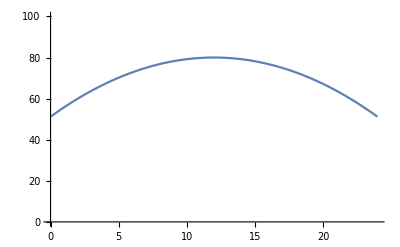

```mathematica
(* In the most realistic model, all Ta, Tw, and P are variable. For simplicity, we are only going to model one period, t=0:24. Keep our previous Tw, as a business decreasing its heating or cooling outside of business hours is common. Ta is a simple quadratic, as the world is coolest at night, then warms up as the sun is out, only to cool again in the evening.*)
Clear[Ta,P]
Ta[t_] := -(1/5)(t-12)^2 + 80  ;
Plot[Ta[t],{t,0,24},PlotRange->{0,100}]
```

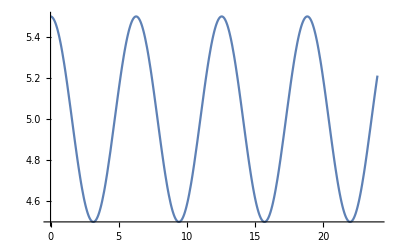

```mathematica
(* P is a simple periodic cos function. Whether it be due to cooldown time or demand for electricity elsewhere, HVAC systems don't run at full throttle constantly, but periodically change the degree to which they run.*)
P[t_] := 0.5Cos[t]+5;
Plot[P[t],{t,0,24}]
```

```mathematica
Temp4 =T4'[t] == k1(T4[t]-Ta[t]) + k2(T4[t]-TW[t]) + P[t];
```

```mathematica
sol4 = NDSolve[{Temp4,T4[0] == 65},T4[t],{t,0,24}]
```

{{T4[t]→InterpolatingFunction[…][t]}}

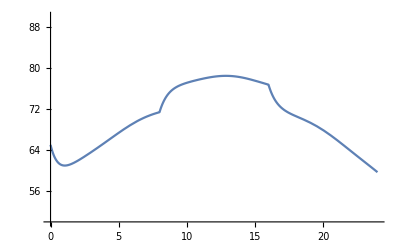

```mathematica
Plot[Evaluate[T4[t]]/.sol4,{t,0,24},PlotRange->{50,90}]
```

```mathematica
(* Again, we can clearly see when our Tw increases and decreases, and we see how the temperature of the building rises and falls with Ta*)
```